## First we read in all six values

```mathematica
all6=Get["D:\\Saved\\allGraphs6-realnull.m"];
```

```mathematica
Length[all6]
```

53071

We calculate the six atoms, which is those with a colofour of one variable in the null base

```mathematica
sixAtoms=Select[Keys[all6],Length[ListofVars[all6[#,"colofourrealnull"]]]==1&];Length[sixAtoms]
```

203

## Now we map the six atoms to the five atoms

The following formula applies the rule to get the corresponding five atom.  If “6” is alone, we multiply by 4, else we just take the corresponding value

```mathematica
DropSix[symbol_]:=Block[{name=SymbolName[symbol]},
If[StringEndsQ[name,"x6"],
4*Symbol[StringDrop[name,-2]],
Symbol[StringDelete[name,"6"]]
]
]
```

Calculate the corresponding value of each six atom to the five atom in the null base.

```mathematica
rep6To5=Table[all6[k,"colofourrealnull"]->DropSix[all6[k,"colofourrealnull"]],{k,sixAtoms}];
```

## Compute a new colofour formula for all six graphs and save it

```mathematica
Monitor[Table[all6[k,"colo4"]=Expand[Simplify[(all6[k,"colofourrealnull"]/.rep6To5)]],{k,Sort[Keys[all6]]}],k];
```

{4 n1x2x3x4x5,3 n1x2x3x4x5,n1x2x3x4x5,3 n1x2x3x4x5,n1x2x3x45+2 n1x2x3x4x5,n1x2x3x4x5,-4 n1x2x3x45+4 n1x2x3x4x5,-3 n1x2x3x45+3 n1x2x3x4x5,-3 n1x2x3x45+3 n1x2x3x4x5,-2 n1x2x3x45+2 n1x2x3x4x5,-n1x2x3x45+n1x2x3x4x5,-n1x2x3x45+n1x2x3x4x5,4 n1x2x3x45,3 n1x2x3x45,n1x2x3x45,3 n1x2x3x4x5,n1x2x35x4+2 n1x2x3x4x5,n1x2x34x5+2 n1x2x3x4x5,-n1x2x345+n1x2x34x5+n1x2x35x4+n1x2x3x45+n1x2x3x4x5,53034,-2 n12345+2 n1235x4,-n12345+n1235x4,-n12345+n1235x4,4 n1234x5,3 n1234x5,n1234x5,3 n1234x5,n12345+2 n1234x5,n1234x5,-4 n12345+4 n1234x5,-3 n12345+3 n1234x5,-3 n12345+3 n1234x5,-2 n12345+2 n1234x5,-n12345+n1234x5,-n12345+n1234x5,4 n12345,3 n12345,n12345}
 |  |  |  |

```mathematica
Put[all6,"D:\\Saved\\allGraphs6-realnull4.m"]
```

## Verify that the formulas are still correct.

For this we need the colofour of the five atoms in null base

```mathematica
repFive=Table[allGraphs[k,"colofourrealnull"]->ChromaticPolynomial[allGraphs[k,"graph"],4],{k,realyNullAtomKeys}];
```

We will now calculate the six graphs colofour by using the graph and by using the formula based on the five atom values.  Both should be the same.

```mathematica
t345=Monitor[Table[ChromaticPolynomial[all6[k,"graph"],4]-(all6[k,"colo4"]/.repFive),{k,Sort[Keys[all6]]}],k];
```

The total of all differences should be zero, which is another way to say that they should all be equal

```mathematica
Total[Abs[t345]]
```

0

## Small experiment to see if some formulas have become shorter; they have

Here we select formulas that are now written in 2 variables while they used to be written in more

```mathematica
t456=Select[Keys[all6],(Length[ListofVars[all6[#,"colo4"]]]==2 )&& (Length[ListofVars[all6[#,"colofourrealnull"]]]!=2)&]
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListQ::argx will be suppressed during this calculation.

```mathematica
Length[t456]
```

955

```mathematica
Table[Length[ListofVars[all6[k,"colofourrealnull"]]],{k,t456}]//Tally//Sort
```

{{4,705},{5,160},{52,15},{104,20},{141,30},{168,20},{188,5}}

```mathematica
all6[4782969,"graph"]
```

-Graphics-

```mathematica
Select[Table[Simplify[all6[k,"colofourrealnull"]/.rep6To5]//Expand,{k,Take[Keys[all6],5]}],Length[ListofVars[]]==2&]
```

{4 n1x2x3x4x5,-4 n12x3x4x5+4 n1x2x3x4x5,4 n123x4x5-4 n12x3x4x5-4 n13x2x4x5+4 n1x2x3x4x5,-4 n1234x5+4 n123x4x5+4 n124x3x5-4 n12x3x4x5+4 n134x2x5-4 n13x2x4x5-4 n14x2x3x5+4 n1x2x3x4x5,4 n12345-4 n1234x5-4 n1235x4+4 n123x4x5-4 n1245x3+4 n124x3x5+4 n125x3x4-4 n12x3x4x5-4 n1345x2+4 n134x2x5+4 n135x2x4-4 n13x2x4x5+4 n145x2x3-4 n14x2x3x5-4 n15x2x3x4+4 n1x2x3x4x5}

```mathematica
Length[DeleteDuplicates[Table[all6[k,"colo4"],{k,Sort[Keys[all6]]}]]]
```

31008

```mathematica
Select[FactorList[n1x2x3x45+2 n1x2x3x4x5],!NumberQ[#[[1]]]&]
```

{{n1x2x3x45+2 n1x2x3x4x5,1}}

## Now we look at the formulas in the complete graphs

First get a mapping of null to complete for the five atoms;

```mathematica
rep5Complete=Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"colofour"],{k,realyNullAtomKeys}];
```

Now get a mapping of the six atoms written in the five atoms full base

```mathematica
rep6Null=Table[all6[k,"colofourrealnull"]->(all6[k,"colo4"]/.rep5Complete)//Expand,{k,sixAtoms}];
```

```mathematica
Expand[all6[0,"colofourrealnull"]/.rep6Null]/.repcolofourgraph2
```

4 -Graphics-v1234559048+4 -Graphics-v1234x558288+4 -Graphics-v1235x456770+4 -Graphics-v123x4556012+4 -Graphics-v1245x352232+4 -Graphics-v125x3449972+4 -Graphics-v12x34549220+4 -Graphics-v124x3551478+4 -Graphics-v1345x239014+4 -Graphics-v145x2332684+4 -Graphics-v15x23430586+4 -Graphics-v1x234529888+4 -Graphics-v14x23531984+4 -Graphics-v135x2436898+4 -Graphics-v13x24536194+4 -Graphics-v134x2538308+4 -Graphics-v123x4x556011+4 -Graphics-v124x3x551475+4 -Graphics-v12x34x549216+4 -Graphics-v125x3x449963+4 -Graphics-v12x35x449210+4 -Graphics-v12x3x4549208+4 -Graphics-v134x2x538281+4 -Graphics-v14x23x531954+4 -Graphics-v1x234x529857+4 -Graphics-v13x24x536166+4 -Graphics-v135x2x436817+4 -Graphics-v15x23x430496+4 -Graphics-v1x235x429797+4 -Graphics-v13x25x436112+4 -Graphics-v13x2x4536086+4 -Graphics-v1x23x4529768+4 -Graphics-v145x2x332441+4 -Graphics-v15x24x330334+4 -Graphics-v1x245x329633+4 -Graphics-v14x25x331738+4 -Graphics-v15x2x3430262+4 -Graphics-v1x25x3429560+4 -Graphics-v1x2x34529537+4 -Graphics-v14x2x3531714+4 -Graphics-v1x24x3529608+4 -Graphics-v12x3x4x549207+4 -Graphics-v13x2x4x536085+4 -Graphics-v1x23x4x529767+4 -Graphics-v14x2x3x531711+4 -Graphics-v1x24x3x529605+4 -Graphics-v1x2x34x529533+4 -Graphics-v15x2x3x430253+4 -Graphics-v1x25x3x429551+4 -Graphics-v1x2x3x4529525+4 -Graphics-v1x2x35x429527+4 -Graphics-v1x2x3x4x529524

## Now look at the six graphs that are zero. We look at they corresponding 5 complete base formulas to see that they are indeed all 0 or K5

Get the keys of 6 graphs that have a zero colofour.  We do this directly by looking at their graphs.

```mathematica
zero6Keys=Select[Keys[all6],ChromaticPolynomial[all6[#,"graph"],4]==0&];Length[zero6Keys]
```

187

Now we look at their formulas

```mathematica
Table[((all6[k,"colofourrealnull"]/.rep6Null)//Expand),{k,zero6Keys}]
```

{v1x2x3x4x5,0,-v1x2x3x4x5,v1x2x3x4x5,v1x2x3x4x5,0,0,0,-v1x2x3x4x5,0,v1x2x3x4x5,2 v1x2x3x4x5,v1x2x3x4x5,0,v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,v1x2x3x4x5,2 v1x2x3x4x5,v1x2x3x4x5,0,v1x2x3x4x5,3 v1x2x3x4x5,2 v1x2x3x4x5,v1x2x3x4x5,2 v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,v1x2x3x4x5,2 v1x2x3x4x5,v1x2x3x4x5,0,v1x2x3x4x5,3 v1x2x3x4x5,2 v1x2x3x4x5,v1x2x3x4x5,2 v1x2x3x4x5,3 v1x2x3x4x5,2 v1x2x3x4x5,v1x2x3x4x5,2 v1x2x3x4x5,4 v1x2x3x4x5,3 v1x2x3x4x5,2 v1x2x3x4x5,3 v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0,-v1x2x3x4x5,0}

## Now look at the six graphs that are zero. We look at they corresponding 5 complete base formulas to see that they are indeed all 0 or K5

```mathematica
Table[Length[ListofVars[all6[k,"colo4"]]],{k,Keys[all6]}]//Tally//Sort
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListQ::argx will be suppressed during this calculation.

{{1,354},{2,1660},{4,3675},{5,1560},{7,45},{8,5020},{9,225},{10,4530},{11,1065},{12,1215},{13,2700},{14,60},{15,475},{16,3065},{18,390},{19,120},{20,4070},{21,240},{22,1600},{23,180},{24,2165},{25,675},{26,3840},{27,553},{28,390},{29,990},{30,970},{31,1770},{32,550},{33,390},{34,2360},{35,1060},{36,300},{37,410},{38,900},{39,90},{40,1200},{41,390},{42,182},{43,435},{44,65},{45,135},{46,90},{47,480},{48,10},{49,125},{50,45},{51,135},{52,117}}

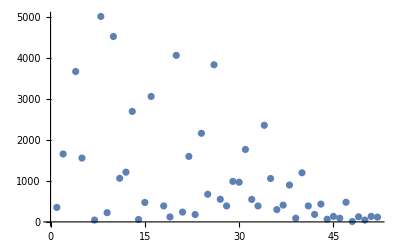

```mathematica
ListPlot[{{1,354},{2,1660},{4,3675},{5,1560},{7,45},{8,5020},{9,225},{10,4530},{11,1065},{12,1215},{13,2700},{14,60},{15,475},{16,3065},{18,390},{19,120},{20,4070},{21,240},{22,1600},{23,180},{24,2165},{25,675},{26,3840},{27,553},{28,390},{29,990},{30,970},{31,1770},{32,550},{33,390},{34,2360},{35,1060},{36,300},{37,410},{38,900},{39,90},{40,1200},{41,390},{42,182},{43,435},{44,65},{45,135},{46,90},{47,480},{48,10},{49,125},{50,45},{51,135},{52,117}}]
```

```mathematica
Select[Keys[all6],Length[ListofVars[all6[#,"colo4"]]]==6&]
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListQ::argx will be suppressed during this calculation.

{7010185,6983941,6971305,7509055,6660427,6625435,6621223,6800467,6446191,6443904,6439366,8584987,8234905,5584495,5575747,5571391,5750635,5396503,5394144,5376388,6109141,5046745,5039686,5026468,11777845,11419339,10343407,2391637,2391313,2391169,2566201,2216281,2211816,2184934,2916283,1866523,1853146,1830802,3966115,816835,777118,767992,27094,22882,9832}

```mathematica
all6[7010185,"colo4"]
```

2 n12345-n1234x5-n1235x4-n145x23+n15x23x4-n1x2345+n1x234x5

```mathematica
all6[7010185,"colo4"]/.repFive
```

72

```mathematica
Table[k->(k/.repFive),{k,ListofVars[all6[7010185,"colo4"]]}]
```

{n15x23x4→64,n1x234x5→64,n12345→4,n1234x5→16,n1235x4→16,n145x23→16,n1x2345→16}

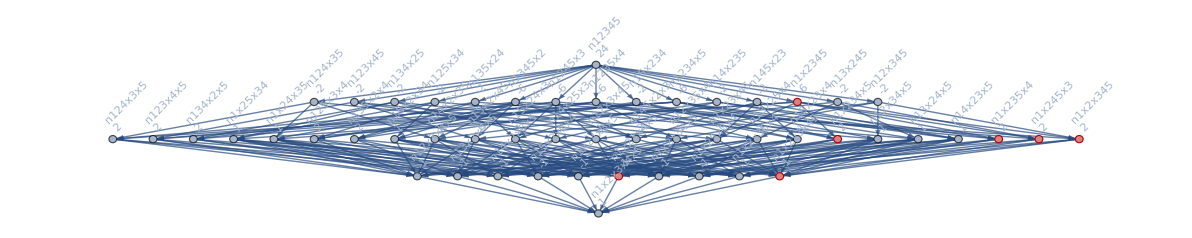

```mathematica
Graph[MobiusGraph2[k5Key],GraphHighlight->ListofVars[all6[9832,"colo4"]],GraphHighlightStyle->"Dashed"]
```

```mathematica
Formule[x_]:=Sort[Tally[Map[StringCount[SymbolName[#],"x"]&,ListofVars[x]]]]
```

```mathematica
Formule[2 n12345-n1234x5-n1235x4-n145x23+n15x23x4-n1x2345+n1x234x5]
```

{{0,1},{1,4},{2,2}}

```mathematica
Select[Keys[all6],((all6[#,"colo4"]/.repFive))==4&]
```

{14348906}

```mathematica
all6[14348906,"colo4"]
```

n12345

## Lets not make a difference between different K3 versions

```mathematica
rep5CompleteReduced=Table[allGraphs[k,"colofour"]->Symbol["K"<>ToString[VertexCount[allGraphs[k,"graph"]]]],{k,atomKeys}]
```

{v1x2x3x4x5→K5,v1x2x3x45→K4,v1x2x35x4→K4,v1x2x34x5→K4,v1x2x345→K3,v1x25x3x4→K4,v1x25x34→K3,v1x24x3x5→K4,v1x24x35→K3,v1x245x3→K3,v1x23x4x5→K4,v1x23x45→K3,v1x235x4→K3,v1x234x5→K3,v1x2345→K2,v15x2x3x4→K4,v15x2x34→K3,v15x24x3→K3,v15x23x4→K3,v15x234→K2,v14x2x3x5→K4,v14x2x35→K3,v14x25x3→K3,v14x23x5→K3,v14x235→K2,v145x2x3→K3,v145x23→K2,v13x2x4x5→K4,v13x2x45→K3,v13x25x4→K3,v13x24x5→K3,v13x245→K2,v135x2x4→K3,v135x24→K2,v134x2x5→K3,v134x25→K2,v1345x2→K2,v12x3x4x5→K4,v12x3x45→K3,v12x35x4→K3,v12x34x5→K3,v12x345→K2,v125x3x4→K3,v125x34→K2,v124x3x5→K3,v124x35→K2,v1245x3→K2,v123x4x5→K3,v123x45→K2,v1235x4→K2,v1234x5→K2,v12345→K1}

```mathematica
Select[Keys[all6],With[
{formula=Expand[all6[#,"colo4"]/.rep5Complete/.rep5CompleteReduced]},
Table[Coefficient[formula,m],{m,{K1,K2,K3,K4}}]=={0,0,0,1}
]&
]
```

{7174440,7174458,7174466,7174446,7174442,7174471,7174489,7174435,7174416,7174417,7174414,7174531,7174537,7174562,7174506,7174368,7174375,7174369,7174360,7174398,7174344,7174346,7174342,7174336,7174695,7174697,7174726,7174666,7174206,7174209,7174211,7174200,7174234,7174182,7174186,7174180,7174174,7174128,7174126,7175173,7175191,7175263,7175101,7175425,7174939,7173733,7173714,7173715,7173712,7173805,7173642,7173643,7173616,7173967,7173481,7173478,7173454,7176637,7176643,7176667,7176613,7177370,7175910,7172262,7172269,7172263,7172254,7172293,7172238,7172239,7172158,7172994,7171536,7171538,7171534,7171528,7171510,7171456,7181013,7181015,7181041,7180987,7181746,7180282,7167888,7167891,7167893,7167882,7167919,7167865,7167862,7167622,7168618,7167162,7167166,7167160,7167154,7167136,7166920,7165704,7165702,7194135,7194137,7194139,7194133,7194892,7193380,7154769,7154771,7154773,7154767,7154742,7154740,7154688,7154524,7155472,7154040,7154038,7154068,7154014,7153960,7153798,7152582,7152556,7148206,7148182,7233493,7233511,7233583,7233421,7233745,7233259,7235689,7231315,7240063,7226941,7253185,7213819,7115413,7115394,7115395,7115392,7115485,7115322,7115323,7115296,7115647,7115161,7115158,7115134,7117591,7113216,7113217,7112488,7121965,7108843,7108840,7108114,7135087,7095721,7095694,7094992,7351597,7351603,7351627,7351573,7352329,7350871,7410650,7292550,6997302,6997309,6997303,6997294,6997333,6997278,6997279,6997198,6998035,6996576,6996577,6994390,7056354,6938256,6938258,6938254,6938248,6938230,6938176,6937528,6936070,7705893,7705895,7705921,7705867,7706623,7705165,7764946,7646842,6643008,6643011,6643013,6643002,6643039,6642985,6642982,6642742,6643741,6642283,6642280,6635722,6702058,6583962,6583966,6583960,6583954,6583936,6583720,6583234,6577402,6465864,6465862,8768775,8768777,8768779,8768773,8769505,8768047,8827852,8709700,5580129,5580131,5580133,5580127,5580102,5580100,5580048,5579884,5580859,5579401,5579374,5559718,5639152,5521080,5521078,5521108,5521054,5521000,5520838,5520352,5501398,5402982,5402956,5048686,5048662,11957421,11957423,11957425,11957419,11957449,11957395,12017200,11897644,2391483,2391485,2391487,2391481,2391511,2391457,2390754,2390752,2390728,2389296,2384920,2371774,2449804,2332434,2332432,2332408,2333164,2331706,2330248,2325874,2312752,2214336,2213608,1860040,1859314,797134,796432}

```mathematica
ChromaticPolynomial[all6[2389296,"graph"],4]
```

24

```mathematica
all6[2389296,"colo4"]
```

-6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1245x3+n124x35-n124x3x5+n125x34-n125x3x4+2 n12x345-n12x34x5-n12x35x4-n12x3x45+n12x3x4x5

```mathematica
all6[2389296,"colofour"]
```

v12x3x4x56+v12x3x4x5x6+v1x25x3x4x6+v1x2x3x4x56+v1x2x3x4x5x6

```mathematica
Expand[all6[2389296,"colo4"]/.rep5Complete]
```

v12x3x4x5

```mathematica
all6[2389296,"graph"]
```

-Graphics-

```mathematica
Expand[all6[2389296,"colo4"]/.rep5Complete]/.repcolofourgraph2
```

-Graphics-v12x3x4x549207

```mathematica
all6[2389296,"colofourrealnull"]
```

-54 n123456+12 n12345x6+18 n12346x5-4 n1234x5x6+8 n12356x4+2 n1235x46-2 n1235x4x6+4 n1236x45-4 n1236x4x5+n123x456-n123x45x6-n123x46x5+n123x4x5x6+8 n12456x3+2 n1245x36-2 n1245x3x6+4 n1246x35-4 n1246x3x5+n124x356-n124x35x6-n124x36x5+n124x3x5x6+n1256x34-n1256x3x4+2 n126x345-n126x34x5-n126x35x4-n126x3x45+n126x3x4x5+18 n13456x2+6 n1345x26-6 n1345x2x6-6 n1346x2x5-2 n134x26x5+2 n134x2x5x6+4 n1356x24-4 n1356x2x4+4 n135x246-2 n135x24x6-2 n135x26x4-2 n135x2x46+2 n135x2x4x6+2 n136x245-2 n136x24x5-2 n136x2x45+2 n136x2x4x5+2 n13x2456-n13x245x6-2 n13x246x5+n13x24x5x6-n13x26x45+n13x26x4x5-n13x2x456+n13x2x45x6+n13x2x46x5-n13x2x4x5x6+4 n1456x23-4 n1456x2x3+4 n145x236-2 n145x23x6-2 n145x26x3-2 n145x2x36+2 n145x2x3x6+2 n146x235-2 n146x23x5-2 n146x2x35+2 n146x2x3x5+2 n14x2356-n14x235x6-2 n14x236x5+n14x23x5x6-n14x26x35+n14x26x3x5-n14x2x356+n14x2x35x6+n14x2x36x5-n14x2x3x5x6+2 n156x234-n156x23x4-n156x24x3-n156x2x34+n156x2x3x4+6 n15x2346-2 n15x234x6-2 n15x236x4-n15x23x46+n15x23x4x6-2 n15x246x3-n15x24x36+n15x24x3x6-n15x26x34+n15x26x3x4-2 n15x2x346+n15x2x34x6+n15x2x36x4+n15x2x3x46-n15x2x3x4x6+4 n16x2345-2 n16x234x5-n16x235x4-n16x23x45+n16x23x4x5-n16x245x3-n16x24x35+n16x24x3x5-2 n16x2x345+n16x2x34x5+n16x2x35x4+n16x2x3x45-n16x2x3x4x5+12 n1x23456-4 n1x2345x6-6 n1x2346x5+2 n1x234x5x6-2 n1x2356x4-n1x235x46+n1x235x4x6-2 n1x236x45+2 n1x236x4x5-n1x23x456+n1x23x45x6+n1x23x46x5-n1x23x4x5x6-2 n1x2456x3-n1x245x36+n1x245x3x6-2 n1x246x35+2 n1x246x3x5-n1x24x356+n1x24x35x6+n1x24x36x5-n1x24x3x5x6-2 n1x26x345+n1x26x34x5+n1x26x35x4+n1x26x3x45-n1x26x3x4x5-4 n1x2x3456+2 n1x2x345x6+2 n1x2x346x5-n1x2x34x5x6+n1x2x356x4+n1x2x35x46-n1x2x35x4x6+n1x2x36x45-n1x2x36x4x5+n1x2x3x456-n1x2x3x45x6-n1x2x3x46x5+n1x2x3x4x5x6

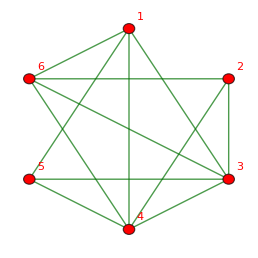

```mathematica
all6[2389296,"graph"]
```

```mathematica
4+60*4+100*16+40*64
```

4404

```mathematica
CoefficientList[Expand[all6[0,"colo4"]/.rep5Complete/.rep5CompleteReduced],{K1,K2,K3,K4,K5}]
```

{{{{{0,4},{40,0}},{{100,0},{0,0}}},{{{60,0},{0,0}},{{0,0},{0,0}}}},{{{{4,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}}}

```mathematica
Expand[all6[0,"colo4"]/.rep5Complete/.rep5CompleteReduced]
```

4 K1+60 K2+100 K3+40 K4+4 K5

## We are searching for graphs with 6 nodes that have a multiple of K5 as a formula.

```mathematica
sixWithOneVar=Select[Keys[all6],With[
{formula=Expand[all6[#,"colo4"]/.rep5Complete]},
DeleteDuplicates[ListofVars[formula]]=={v1x2x3x4x5}
]&
];
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListQ::argx will be suppressed during this calculation.

```mathematica
sixWithOneVar2=Select[Keys[all6],With[
{formula=Expand[all6[#,"colo4"]/.rep5Complete]},
formula==0
]&
];
```

```mathematica
Table[VertexDegree[all6[k,"graph"],6]->Expand[all6[k,"colo4"]/.rep5Complete],{k,sixWithOneVar}]//TableForm
```

3→v1x2x3x4x5
5→-v1x2x3x4x5
VertexDegree[-Graphics-,6]→v1x2x3x4x5
VertexDegree[-Graphics-,6]→v1x2x3x4x5
5→-v1x2x3x4x5
VertexDegree[-Graphics-,6]→v1x2x3x4x5
2→2 v1x2x3x4x5
3→v1x2x3x4x5
3→v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
VertexDegree[-Graphics-,6]→v1x2x3x4x5
2→2 v1x2x3x4x5
3→v1x2x3x4x5
3→v1x2x3x4x5
1→3 v1x2x3x4x5
2→2 v1x2x3x4x5
3→v1x2x3x4x5
2→2 v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
VertexDegree[-Graphics-,6]→v1x2x3x4x5
2→2 v1x2x3x4x5
3→v1x2x3x4x5
3→v1x2x3x4x5
1→3 v1x2x3x4x5
2→2 v1x2x3x4x5
3→v1x2x3x4x5
2→2 v1x2x3x4x5
1→3 v1x2x3x4x5
2→2 v1x2x3x4x5
3→v1x2x3x4x5
2→2 v1x2x3x4x5
0→4 v1x2x3x4x5
1→3 v1x2x3x4x5
2→2 v1x2x3x4x5
1→3 v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5
5→-v1x2x3x4x5